Sapphire
Q^-1vsL

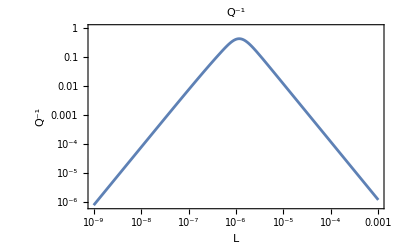

```mathematica
QwoHeatFlow =δE Abs[ 6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) ]/.
{δE->0.88,ξ->1.3 10^-6/L};
QHeatFlowg=LogLogPlot[QwoHeatFlow,{L,0.000000001,0.001},PlotLabel->"Q^-1", Frame->True,FrameLabel->{L,"Q^-1"}]
```

```mathematica
QHeatFlow=δE Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.{δE->0.88,ξ->1.3 10^-6/L}; (*sapphire*)
```

d=1.1,1.3,1.7

3.0041×10^17 Abs[(L^3 (-(2.6×10^-6 (Cos[(2.73×10^-6)/L] Cosh[(1.3×10^-7)/L]+Cos[(1.3×10^-7)/L] Cosh[(2.73×10^-6)/L]))/L-Cosh[(2.73×10^-6)/L] Sin[(1.3×10^-7)/L]+Cosh[(1.3×10^-7)/L] Sin[(2.73×10^-6)/L]-Cos[(2.73×10^-6)/L] Sinh[(1.3×10^-7)/L]+Cos[(1.3×10^-7)/L] Sinh[(2.73×10^-6)/L]))/(Cos[(2.86×10^-6)/L]+Cosh[(2.86×10^-6)/L])]

3.0041×10^17 Abs[(L^3 (-(2.6×10^-6 (Cos[(2.99×10^-6)/L] Cosh[(3.9×10^-7)/L]+Cos[(3.9×10^-7)/L] Cosh[(2.99×10^-6)/L]))/L-Cosh[(2.99×10^-6)/L] Sin[(3.9×10^-7)/L]+Cosh[(3.9×10^-7)/L] Sin[(2.99×10^-6)/L]-Cos[(2.99×10^-6)/L] Sinh[(3.9×10^-7)/L]+Cos[(3.9×10^-7)/L] Sinh[(2.99×10^-6)/L]))/(Cos[(3.38×10^-6)/L]+Cosh[(3.38×10^-6)/L])]

3.0041×10^17 Abs[(L^3 (-(2.6×10^-6 (Cos[(3.51×10^-6)/L] Cosh[(9.1×10^-7)/L]+Cos[(9.1×10^-7)/L] Cosh[(3.51×10^-6)/L]))/L-Cosh[(3.51×10^-6)/L] Sin[(9.1×10^-7)/L]+Cosh[(9.1×10^-7)/L] Sin[(3.51×10^-6)/L]-Cos[(3.51×10^-6)/L] Sinh[(9.1×10^-7)/L]+Cos[(9.1×10^-7)/L] Sinh[(3.51×10^-6)/L]))/(Cos[(4.42×10^-6)/L]+Cosh[(4.42×10^-6)/L])]

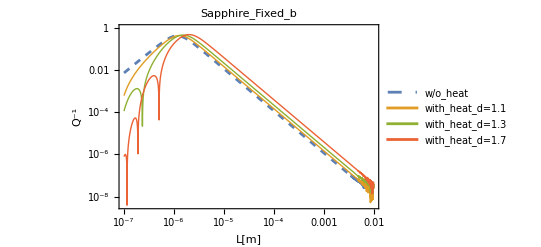

```mathematica
Q11=QHeatFlow/.{d->1.1}
Q13=QHeatFlow/.{d->1.3}
Q17=QHeatFlow/.{d->1.7}
HeatFlowg=LogLogPlot[{QwoHeatFlow,Q11,Q13,Q17},{L,0.0000001,0.01},PlotLabel->"Sapphire_Fixed_b", Frame->True,FrameLabel->{"L[m]","Q^-1"},PlotLegends->Placed[{"w/o_heat","with_heat_d=1.1","with_heat_d=1.3","with_heat_d=1.7"},{0.4,0.25}],GridLinesStyle->LightGray,GridLines->Full,PlotStyle->{Dashed,Thick,Thick,Thick}]
```